## Лабароторная работа №3 Дунаев Виктор Андреевич 3 Курс, 6 Группа Вариант 3

## Task 1

## С помощью формул Симпсона и Гаусса вычислить интеграл с точностью до 10^-6. Сравнить полученные результаты и результат вычисления с помощью встроенной функции. Должны быть собственные функции, аргументами которых являются интегрируемая функция и интервал. Кроме значений интеграла должно выводиться количество итераций, необходимых для вычисления. В формуле Гаусса для получения полиномов Лежандра должна быть написана собственная функция.

```mathematica
N[∫_-1^9 (ⅇ^(x-7)-1)/(x^2+7)ⅆx]
```

-0.512428+1.04906×10^-17 ⅈ

```mathematica
function[x_] := (ⅇ^(x-7)-1)/(x^2+7)
```

```mathematica
N[∫_-1^9 function[x]ⅆx]
```

-0.512428+1.04906×10^-17 ⅈ

```mathematica
simpson[f_, a_, b_, twoN_]:=
(
h= (b-a)/twoN;
sum = 0;
sum += f[a]+f[b];
sum +=2*∑_(i=1)^(twoN/2 -1) f[(a+2*i*h)]+4*∑_(i=1)^(twoN/2) f[(a+(2*i-1)*h)];
sum *= h/3;
N[sum]
)
```

```mathematica
simpsonIterations[fu_, a_, b_]:=
(
twoN = 2;
prev = simpson[fu, a, b, twoN];
twoN *=2;
next =simpson[fu, a, b, twoN];
While[Abs[next - prev] >15* 10^-6,
prev = next;
twoN *= 2;
next = simpson[fu, a, b, twoN];];
Print ["Количество итераций: ", Log[2, twoN]];
next
)
```

```mathematica
simpsonIterations[function, -1, 9]
```

Количество итераций: 5

-0.512427

```mathematica
(* Метол Гаусса *)
```

```mathematica
legendre[n_]:=
(
1/(2^n*Factorial[n])D[(x^2 -1)^n, {x, n}]
)
```

```mathematica
getLegendreRoots[poly_]:=
(
Solve[poly == 0, x]
)
```

```mathematica
gauss[func_, a_, b_, deg_]:=
(
repl = {};
coefList = {};
roots = Flatten[getLegendreRoots[legendre[deg]]];
For[i=1, i ≤  deg , i++,
AppendTo[repl, (b+a)/2+(b-a)/2*x/.roots⟦i⟧];
AppendTo[coefList, 2/((1-x^2)*D[legendre[deg], x]^2)/.roots⟦i⟧]

];
sum = (b-a)/2*∑_(i=1)^deg coefList⟦i⟧*func[repl⟦i⟧]
)
```

```mathematica
gaussIterations[func_, a_, b_]:=
(
degr = 2;
counter = 1;
first = gauss[func, a, b, 2];
sec = gauss[func, a, b, 4];
While[Abs[N[first-sec]/(1-(1/2)^4)]≥10^-6,degr++;
Print[counter];
counter++;
first = sec;
sec=gauss[func,a,b,degr]];
Print ["Количество итераций: ", counter];
N[sec]
)
```

```mathematica
gaussIterations[function, -1, 9]
```

1

2

3

4

5

6

7

8

9

10

Количество итераций: 11

-0.512428

## Task 2

## Методами деления отрезка пополам и золотого сечения вычислить максимум и минимум функции на заданном интервале с точностью до 10^-6. Сравнить полученные результаты и результат вычисления с помощью встроенных функций Maximize и Minimize. Должны быть собственные функции, аргументами которых являются заданная функция и интервал. Выводиться должно количество итераций, требуемых для вычисления min и max, и {x_min,min(f(x))},{x_max,max(f(x))} . Точки максимума и минимума должны быть изображены графически.

```mathematica
(* f(x)=-x^3+3 x^2-x+5-sin(x^4),x∈[27/20,7/4] *)
(* A - золотое сечение*)
```

```mathematica
func[x_]:= -x^3+3 x^2-x+5-Sin[x^4]
```

```mathematica
func[x]
```

5-x+3 x^2-x^3-Sin[x^4]

```mathematica
N[Minimize[{func[x], x≤ 7/4, x≥ 27/20}, x]]
```

{6.04128,{x→1.67223}}

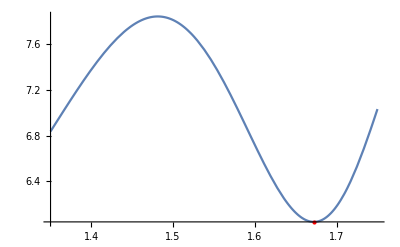

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{x,func[x]}/.Last[%]]}]]
```

```mathematica
N[Maximize[{func[x], x≤ 7/4, x≥ 27/20}, x]]
```

{7.84588,{x→1.48117}}

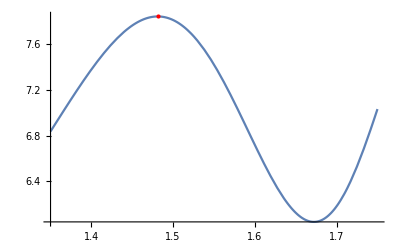

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{x,func[x]}/.Last[%]]}]]
```

```mathematica
goldenSection[f_, a_, b_, max_]:=
(
counter = 0;
low = a;
top = b;
ef = (1+Sqrt[5])/2;
While [Abs[top - low]> 10^-6, 
counter++;
x1 = top - (top-low)/ef;
x2= low+(top-low)/ef;
f1 = f[x1];
f2 = f[x2];
rule = f1≥ f2;
If[max == true, rule = f1≤ f2];
If[rule, low = x1, top = x2];
];
Print ["Количество итераций: ",counter];
N[(low + top)/2]
)
```

```mathematica
goldenMax[f_, a_, b_]:=goldenSection[f, a, b, true]
```

```mathematica
goldenMin[f_, a_, b_]:=goldenSection[f, a, b, false]
```

```mathematica
maxX = goldenMax[func, 27/20, 7/4]
```

Количество итераций: 27

1.48117

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{maxX, func[maxX]}]}]]
```

-Graphics-

```mathematica
minX = goldenMin[func,27/20, 7/4]
```

Количество итераций: 27

1.67223

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{minX, func[minX]}]}]]
```

-Graphics-

```mathematica
(* Б - Метод половинного деления *)
```

```mathematica
bisection[f_, a_, b_, max_]:=
(
counter = 0;
eps = 10^-6;
low = a;
top = b;
While [Abs[top - low]> 10^-6, 
c  = (low + top)/2;
counter++;
f1 = f[c-eps];
f2 = f[c+eps];
rule = f1≥ f2;
If[max == true, rule = f1≤ f2];
If[rule, low = c, top = c]];
Print ["Количество итераций: ",counter];
N[(low + top)/2]
)
```

```mathematica
dihMax[f_, a_, b_] := bisection[f, a, b, true]
```

```mathematica
dihMin[f_, a_, b_] := bisection[f, a, b, false]
```

```mathematica
dmax = dihMax[func, 27/20, 7/4]
```

Количество итераций: 19

1.48117

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{dmin, func[dmin]}]}]]
```

-Graphics-

```mathematica
dmin = dihMin[func, 27/20, 7/4]
```

Количество итераций: 19

1.67223

```mathematica
Show[Plot[func[x],{x,27/20,7/4}],Graphics[{Red,PointSize[Large], Point[{dmax, func[dmax]}]}]]
```

-Graphics-